```mathematica
CellularAutomaton[110,IntegerDigits[3,2,3]]⟦2⟧
```

1

```mathematica
next[rule_,{a_,b_,c_}]:={a,CellularAutomaton[rule,{a,b,c}]⟦2⟧,c}
```

```mathematica
next[110,{0,0,1}]
```

{0,1,1}

```mathematica
IntegerDigits[7,2,3]
```

{1,1,1}

```mathematica
link=(#->next[110,#])&/@Table[IntegerDigits[i,2,3],{i,0,2^3-1}]
```

{{0,0,0}->{0,0,0},{0,0,1}->{0,1,1},{0,1,0}->{0,1,0},{0,1,1}->{0,1,1},{1,0,0}->{1,0,0},{1,0,1}->{1,1,1},{1,1,0}->{1,1,0},{1,1,1}->{1,0,1}}

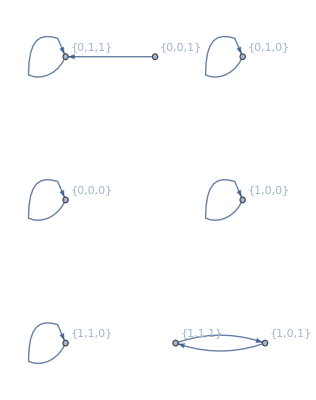

```mathematica
Graph[link,VertexLabels->"Name"]
```

```mathematica
temp=CellularAutomaton[{{0,0,1}->1,{0,1,1}->0,{0,0,0}->0,{1,1,1}->0,{1,0,1}->0,{0,1,0}->0,{1,1,0}->0,{1,0,0}->0}]
```

CellularAutomaton[{{0,0,1}→1,{0,1,1}→0,{0,0,0}→0,{1,1,1}→0,{1,0,1}→0,{0,1,0}→0,{1,1,0}→0,{1,0,0}→0}]

```mathematica
temp[{0,0,1}]
```

{0,1,0}

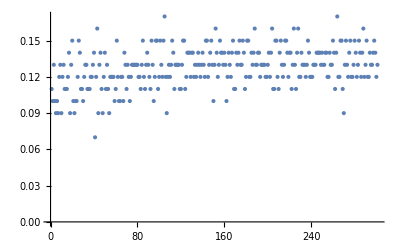

```mathematica
ListPlot[Mean/@temp/@CellularAutomaton[110,RandomInteger[{0,1},100],300]]
```

```mathematica
ans=DSolve[{m l θ''[t]+m g l Sin[θ[t]]==0},θ[t],t]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{θ[t]→-2 JacobiAmplitude[1/2 √((2 g+C[1]) (t+C[2])^2),(4 g)/(2 g+C[1])]},{θ[t]→2 JacobiAmplitude[1/2 √((2 g+C[1]) (t+C[2])^2),(4 g)/(2 g+C[1])]}}

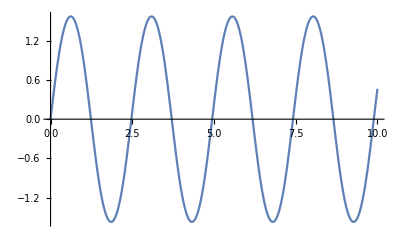

```mathematica
Plot[2 JacobiAmplitude[1/2 √((2 g) (t)^2),(4 g)/(2 g)]/.{g->9},{t,0,10}]
```

```mathematica
CellularAutomaton[110,{0,1,0}]
```

{1,1,0}

```mathematica
rule110=Sum[(c2'[t]-CellularAutomaton[110,IntegerDigits[i,2,3]]⟦2⟧+IntegerDigits[i,2,3]⟦2⟧)(1-(c1[t]-IntegerDigits[i,2,3]⟦1⟧)^2)(1-(c2[t]-IntegerDigits[i,2,3]⟦2⟧)^2)(1-(c3[t]-IntegerDigits[i,2,3]⟦3⟧)^2),{i,0,2^3-1}]//FullSimplify//Expand
```

-2 c3[t]-4 c1[t] c3[t]+4 c1[t]^2 c3[t]+8 c1[t] c2[t] c3[t]-4 c1[t]^2 c2[t] c3[t]+2 c2[t]^2 c3[t]-2 c1[t]^2 c2[t]^2 c3[t]+c3[t]^2+2 c1[t] c3[t]^2-2 c1[t]^2 c3[t]^2-4 c1[t] c2[t] c3[t]^2+2 c1[t]^2 c2[t] c3[t]^2-c2[t]^2 c3[t]^2+c1[t]^2 c2[t]^2 c3[t]^2+c2'[t]+2 c1[t] c2'[t]-2 c1[t]^2 c2'[t]+2 c2[t] c2'[t]+4 c1[t] c2[t] c2'[t]-4 c1[t]^2 c2[t] c2'[t]-2 c2[t]^2 c2'[t]-4 c1[t] c2[t]^2 c2'[t]+4 c1[t]^2 c2[t]^2 c2'[t]+2 c3[t] c2'[t]+4 c1[t] c3[t] c2'[t]-4 c1[t]^2 c3[t] c2'[t]+4 c2[t] c3[t] c2'[t]+8 c1[t] c2[t] c3[t] c2'[t]-8 c1[t]^2 c2[t] c3[t] c2'[t]-4 c2[t]^2 c3[t] c2'[t]-8 c1[t] c2[t]^2 c3[t] c2'[t]+8 c1[t]^2 c2[t]^2 c3[t] c2'[t]-2 c3[t]^2 c2'[t]-4 c1[t] c3[t]^2 c2'[t]+4 c1[t]^2 c3[t]^2 c2'[t]-4 c2[t] c3[t]^2 c2'[t]-8 c1[t] c2[t] c3[t]^2 c2'[t]+8 c1[t]^2 c2[t] c3[t]^2 c2'[t]+4 c2[t]^2 c3[t]^2 c2'[t]+8 c1[t] c2[t]^2 c3[t]^2 c2'[t]-8 c1[t]^2 c2[t]^2 c3[t]^2 c2'[t]

```mathematica
rule30=Sum[(c2'[t]-CellularAutomaton[30,IntegerDigits[i,2,3]]⟦2⟧+IntegerDigits[i,2,3]⟦2⟧)(1-(c1[t]-IntegerDigits[i,2,3]⟦1⟧)^2)(1-(c2[t]-IntegerDigits[i,2,3]⟦2⟧)^2)(1-(c3[t]-IntegerDigits[i,2,3]⟦3⟧)^2),{i,0,2^3-1}]//FullSimplify//Expand
```

-2 c1[t]+c1[t]^2+4 c1[t] c2[t]-2 c1[t]^2 c2[t]-2 c3[t]+2 c1[t]^2 c3[t]+8 c1[t] c2[t] c3[t]-4 c1[t]^2 c2[t] c3[t]+2 c2[t]^2 c3[t]-4 c1[t] c2[t]^2 c3[t]+c3[t]^2+2 c1[t] c3[t]^2-2 c1[t]^2 c3[t]^2-8 c1[t] c2[t] c3[t]^2+4 c1[t]^2 c2[t] c3[t]^2-c2[t]^2 c3[t]^2+2 c1[t] c2[t]^2 c3[t]^2+c2'[t]+2 c1[t] c2'[t]-2 c1[t]^2 c2'[t]+2 c2[t] c2'[t]+4 c1[t] c2[t] c2'[t]-4 c1[t]^2 c2[t] c2'[t]-2 c2[t]^2 c2'[t]-4 c1[t] c2[t]^2 c2'[t]+4 c1[t]^2 c2[t]^2 c2'[t]+2 c3[t] c2'[t]+4 c1[t] c3[t] c2'[t]-4 c1[t]^2 c3[t] c2'[t]+4 c2[t] c3[t] c2'[t]+8 c1[t] c2[t] c3[t] c2'[t]-8 c1[t]^2 c2[t] c3[t] c2'[t]-4 c2[t]^2 c3[t] c2'[t]-8 c1[t] c2[t]^2 c3[t] c2'[t]+8 c1[t]^2 c2[t]^2 c3[t] c2'[t]-2 c3[t]^2 c2'[t]-4 c1[t] c3[t]^2 c2'[t]+4 c1[t]^2 c3[t]^2 c2'[t]-4 c2[t] c3[t]^2 c2'[t]-8 c1[t] c2[t] c3[t]^2 c2'[t]+8 c1[t]^2 c2[t] c3[t]^2 c2'[t]+4 c2[t]^2 c3[t]^2 c2'[t]+8 c1[t] c2[t]^2 c3[t]^2 c2'[t]-8 c1[t]^2 c2[t]^2 c3[t]^2 c2'[t]

```mathematica
rule90=Sum[(c2'[t]-CellularAutomaton[90,IntegerDigits[i,2,3]]⟦2⟧+IntegerDigits[i,2,3]⟦2⟧)(1-(c1[t]-IntegerDigits[i,2,3]⟦1⟧)^2)(1-(c2[t]-IntegerDigits[i,2,3]⟦2⟧)^2)(1-(c3[t]-IntegerDigits[i,2,3]⟦3⟧)^2),{i,0,2^3-1}]//FullSimplify//Expand
```

-2 c1[t]+c1[t]^2+2 c2[t]-2 c1[t]^2 c2[t]-c2[t]^2+2 c1[t] c2[t]^2-2 c3[t]+2 c1[t]^2 c3[t]+8 c1[t] c2[t] c3[t]-4 c1[t]^2 c2[t] c3[t]+2 c2[t]^2 c3[t]-4 c1[t] c2[t]^2 c3[t]+c3[t]^2+2 c1[t] c3[t]^2-2 c1[t]^2 c3[t]^2-2 c2[t] c3[t]^2-4 c1[t] c2[t] c3[t]^2+4 c1[t]^2 c2[t] c3[t]^2+c2'[t]+2 c1[t] c2'[t]-2 c1[t]^2 c2'[t]+2 c2[t] c2'[t]+4 c1[t] c2[t] c2'[t]-4 c1[t]^2 c2[t] c2'[t]-2 c2[t]^2 c2'[t]-4 c1[t] c2[t]^2 c2'[t]+4 c1[t]^2 c2[t]^2 c2'[t]+2 c3[t] c2'[t]+4 c1[t] c3[t] c2'[t]-4 c1[t]^2 c3[t] c2'[t]+4 c2[t] c3[t] c2'[t]+8 c1[t] c2[t] c3[t] c2'[t]-8 c1[t]^2 c2[t] c3[t] c2'[t]-4 c2[t]^2 c3[t] c2'[t]-8 c1[t] c2[t]^2 c3[t] c2'[t]+8 c1[t]^2 c2[t]^2 c3[t] c2'[t]-2 c3[t]^2 c2'[t]-4 c1[t] c3[t]^2 c2'[t]+4 c1[t]^2 c3[t]^2 c2'[t]-4 c2[t] c3[t]^2 c2'[t]-8 c1[t] c2[t] c3[t]^2 c2'[t]+8 c1[t]^2 c2[t] c3[t]^2 c2'[t]+4 c2[t]^2 c3[t]^2 c2'[t]+8 c1[t] c2[t]^2 c3[t]^2 c2'[t]-8 c1[t]^2 c2[t]^2 c3[t]^2 c2'[t]

```mathematica
rule54=Sum[(c2'[t]-CellularAutomaton[54,IntegerDigits[i,2,3]]⟦2⟧+IntegerDigits[i,2,3]⟦2⟧)(1-(c1[t]-IntegerDigits[i,2,3]⟦1⟧)^2)(1-(c2[t]-IntegerDigits[i,2,3]⟦2⟧)^2)(1-(c3[t]-IntegerDigits[i,2,3]⟦3⟧)^2),{i,0,2^3-1}]//FullSimplify//Expand
```

-2 c1[t]+c1[t]^2+4 c1[t] c2[t]-2 c1[t]^2 c2[t]-2 c3[t]-4 c1[t] c3[t]+4 c1[t]^2 c3[t]+4 c2[t] c3[t]+8 c1[t] c2[t] c3[t]-8 c1[t]^2 c2[t] c3[t]+c3[t]^2+4 c1[t] c3[t]^2-3 c1[t]^2 c3[t]^2-2 c2[t] c3[t]^2-8 c1[t] c2[t] c3[t]^2+6 c1[t]^2 c2[t] c3[t]^2+c2'[t]+2 c1[t] c2'[t]-2 c1[t]^2 c2'[t]+2 c2[t] c2'[t]+4 c1[t] c2[t] c2'[t]-4 c1[t]^2 c2[t] c2'[t]-2 c2[t]^2 c2'[t]-4 c1[t] c2[t]^2 c2'[t]+4 c1[t]^2 c2[t]^2 c2'[t]+2 c3[t] c2'[t]+4 c1[t] c3[t] c2'[t]-4 c1[t]^2 c3[t] c2'[t]+4 c2[t] c3[t] c2'[t]+8 c1[t] c2[t] c3[t] c2'[t]-8 c1[t]^2 c2[t] c3[t] c2'[t]-4 c2[t]^2 c3[t] c2'[t]-8 c1[t] c2[t]^2 c3[t] c2'[t]+8 c1[t]^2 c2[t]^2 c3[t] c2'[t]-2 c3[t]^2 c2'[t]-4 c1[t] c3[t]^2 c2'[t]+4 c1[t]^2 c3[t]^2 c2'[t]-4 c2[t] c3[t]^2 c2'[t]-8 c1[t] c2[t] c3[t]^2 c2'[t]+8 c1[t]^2 c2[t] c3[t]^2 c2'[t]+4 c2[t]^2 c3[t]^2 c2'[t]+8 c1[t] c2[t]^2 c3[t]^2 c2'[t]-8 c1[t]^2 c2[t]^2 c3[t]^2 c2'[t]

```mathematica
-FullSimplify[FullSimplify[rule90/.{c2'[t]->c2[t],c2[t]->1/2 c2[t]^2}]/.{c1[t]->c1,c2[t]->c2,c3[t]->c3},{c1≥0,c2≥0,c3≥0}]/.{c1^n_->c1,c2^n_->c2,c3^n_->c3}//FullSimplify
```

c3+1/4 c2 (-9+(-6+4 c2 (1+c2)) c3)+1/2 c1 (2+c2 (-3+2 c2 (1+c2))-8 c3+2 c2 (4+3 c2^3) c3-4 (-1+c2 (2+c2+c2^2)) c3^2)

```mathematica
-FullSimplify[FullSimplify[rule30/.{c2'[t]->c2[t],c2[t]->1/2 c2[t]^2}]/.{c1[t]->c1,c2[t]->c2,c3[t]->c3},{c1≥0,c2≥0,c3≥0}]/.{c1^n_->c1,c2^n_->c2,c3^n_->c3}//FullSimplify
```

1/4 (-6 c2+4 c1 (1+c2 (-3+c2+c2^2))+2 (4-7 c2+2 c1 (-4+c2 (-5+2 c2 (1+c2)))) c3+(-4+13 c2+2 c1 (4+c2 (11-4 c2 (1+c2)))) c3^2)

```mathematica
-FullSimplify[FullSimplify[rule110/.{c2'[t]->c2[t],c2[t]->1/2 c2[t]^2}]/.{c1[t]->c1,c2[t]->c2,c3[t]->c3},{c1≥0,c2≥0,c3≥0}]/.{c1^n_->c1,c2^n_->c2,c3^n_->c3}//FullSimplify
```

(-1+2 (-1+c1) c1) (-2+c3) c3-1/4 c2 (6+(14-13 c3) c3+c1 (12+(38-31 c3) c3)+4 c1^2 (-3+c3 (-8+7 c3)))

```mathematica
-FullSimplify[FullSimplify[rule54/.{c2'[t]->c2[t],c2[t]->1/2 c2[t]^2}]/.{c1[t]->c1,c2[t]->c2,c3[t]->c3},{c1≥0,c2≥0,c3≥0}]/.{c1^n_->c1,c2^n_->c2,c3^n_->c3}//FullSimplify
```

c3-1/2 c2 (3+2 c2 c3)+c1 (-1+c2) (-1-c2 (3+c2)-2 c2 (3+c2) c3+(1+2 c2 (3+c2)) c3^2)

```mathematica
energyFunction[c1_,c2_,c3_]:=c3-1/2 c2 (3+2 c2 c3)+c1 (-1+c2) (-1-c2 (3+c2)-2 c2 (3+c2) c3+(1+2 c2 (3+c2)) c3^2)
```

```mathematica
ene=CellularAutomaton[{{c1_,c2_,c3_}->energyFunction[N@c1,N@c2,N@c3]}]
```

CellularAutomaton[{{c1_,c2_,c3_}→c3-1/2 c2 (3+2 c2 c3)+c1 (-1+c2) (-1-c2 (3+c2)-2 c2 (3+c2) c3+(1+2 c2 (3+c2)) c3^2)}]

```mathematica
energyFunctionC[1,1,1]
```

-1.5

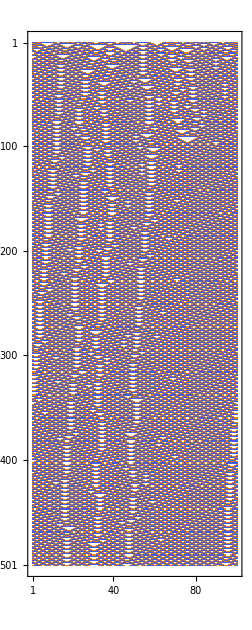

```mathematica
MatrixPlot[ene/@CellularAutomaton[54,RandomInteger[{0,1},100],500]]
```

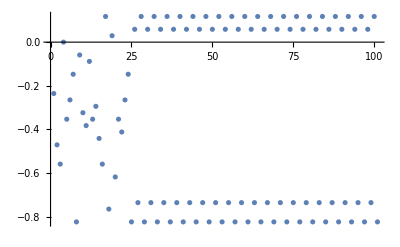

```mathematica
ListPlot[GaussianFilter[Mean/@ene/@N@CellularAutomaton[54,RandomInteger[{0,1},17],100],0],PlotRange->All]
```

### Rule 110

```mathematica
n=10000;
energy=1/n Parallelize@Sum[Mean/@ene/@N@CellularAutomaton[110,RandomInteger[{0,1},100],200],{n}]
```

{-0.406216,-0.632293,-0.504334,-0.469114,-0.508636,-0.47044,-0.498553,-0.506942,-0.505912,-0.496494,-0.504498,-0.51645,-0.503518,-0.509959,-0.517739,-0.513831,-0.517297,-0.518842,-0.520659,-0.519779,-0.519525,-0.521389,-0.521218,-0.519573,-0.521808,-0.525016,-0.520049,-0.521722,-0.523674,-0.522848,-0.522643,-0.523952,-0.523858,-0.522139,-0.524221,-0.525345,-0.523268,-0.525047,-0.525393,-0.524664,-0.523638,-0.525284,-0.52533,-0.525101,-0.525094,-0.526119,-0.525965,-0.525793,-0.525705,-0.527075,-0.525715,-0.525526,-0.52781,-0.527862,-0.526209,-0.526736,-0.527831,-0.527587,-0.526099,-0.527976,-0.527457,-0.527365,-0.526625,-0.528082,-0.528694,-0.52835,-0.528044,-0.528592,-0.527802,-0.52829,-0.528646,-0.528515,-0.528931,-0.528695,-0.528317,-0.528715,-0.52795,-0.528692,-0.528313,-0.528119,-0.529309,-0.528418,-0.528555,-0.527725,-0.529146,-0.529147,-0.529515,-0.528229,-0.528618,-0.529407,-0.530151,-0.529462,-0.528306,-0.528446,-0.529487,-0.530277,-0.530262,-0.529464,-0.529396,-0.529657,-0.529651,-0.529853,-0.530255,-0.529667,-0.529959,-0.529703,-0.529581,-0.529991,-0.530218,-0.529761,-0.530364,-0.531337,-0.529986,-0.530091,-0.530011,-0.529795,-0.530801,-0.531397,-0.529495,-0.530373,-0.530841,-0.530361,-0.530456,-0.531077,-0.530651,-0.530972,-0.530599,-0.531365,-0.529732,-0.530531,-0.53116,-0.531419,-0.530346,-0.530695,-0.531329,-0.530037,-0.530853,-0.531192,-0.530671,-0.53112,-0.531533,-0.530836,-0.530699,-0.530967,-0.531807,-0.531359,-0.531346,-0.531329,-0.530144,-0.531176,-0.531792,-0.531456,-0.530726,-0.531504,-0.531685,-0.531577,-0.531303,-0.531357,-0.531666,-0.531441,-0.531895,-0.531731,-0.531064,-0.53124,-0.531936,-0.531599,-0.531289,-0.531799,-0.532022,-0.531763,-0.531162,-0.532478,-0.531589,-0.531762,-0.532004,-0.532085,-0.532266,-0.531124,-0.531685,-0.531532,-0.532426,-0.532091,-0.531775,-0.531816,-0.532499,-0.531715,-0.531955,-0.532785,-0.531962,-0.531851,-0.532032,-0.532792,-0.532022,-0.532079,-0.532886,-0.532119,-0.532384,-0.532242,-0.532292,-0.532754,-0.53145}

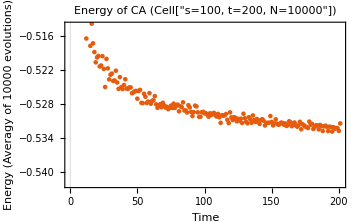

```mathematica
img1=ListPlot[energy,PlotTheme->"Scientific",FrameLabel->{"Time","Energy (Averagy of 10000 evolutions)"},PlotLabel->"Energy of CA (Cell["s=100, t=200, N=10000"])",ImageSize->Medium]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"img","CA110_S100_T200_N10000.pdf"}],img1]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/EnergyInCA/img/CA110_S100_T200_N10000.pdf

### Rule 30

```mathematica
n=10000;
energy=1/n Parallelize@Sum[Mean/@ene/@N@CellularAutomaton[30,RandomInteger[{0,1},17],200],{n}];
```

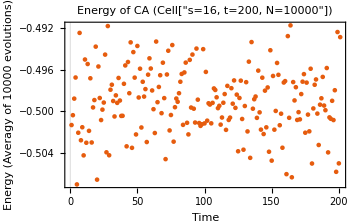

```mathematica
img2=ListPlot[energy,PlotTheme->"Scientific",FrameLabel->{"Time","Energy (Averagy of 10000 evolutions)"},PlotLabel->"Energy of CA (Cell["s=16, t=200, N=10000"])",ImageSize->Medium]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"img","CA030_S17_T200_N10000.pdf"}],img2]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/EnergyInCA/img/CA030_S17_T200_N10000.pdf

### Rule 90

```mathematica
n=10000;
energy=1/n Parallelize@Sum[Mean/@ene/@N@CellularAutomaton[90,RandomInteger[{0,1},17],200],{n}];
```

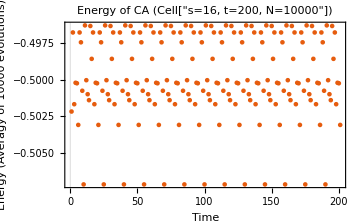

```mathematica
img3=ListPlot[energy,PlotTheme->"Scientific",FrameLabel->{"Time","Energy (Averagy of 10000 evolutions)"},PlotLabel->"Energy of CA (Cell["s=16, t=200, N=10000"])",ImageSize->Medium]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"img","CA090_S17_T200_N10000.pdf"}],img3]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/EnergyInCA/img/CA090_S17_T200_N10000.pdf

### Rule 54

```mathematica
n=10000;
energy=1/n Parallelize@Sum[Mean/@ene/@N@CellularAutomaton[54,RandomInteger[{0,1},50],100],{n}];
```

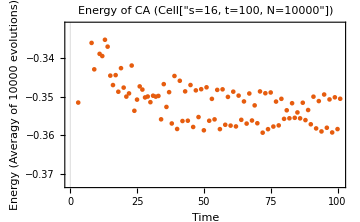

```mathematica
img4=ListPlot[energy,PlotTheme->"Scientific",FrameLabel->{"Time","Energy (Averagy of 10000 evolutions)"},PlotLabel->"Energy of CA (Cell["s=16, t=100, N=10000"])",ImageSize->Medium]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"img","CA054_S17_T200_N10000.pdf"}],img4]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/EnergyInCA/img/CA054_S17_T200_N10000.pdf

## New

```mathematica
EnergyList[list_]:=0Total[#⟦1⟧]+#⟦1⟧.#⟦1⟧-#⟦1⟧.(#⟦2⟧-#⟦1⟧)&/@Partition[list-0.5,2,1]
```

```mathematica
EnergyList[list_]:=-#⟦1⟧.#⟦2⟧&/@Partition[2list-1,2,1]
```

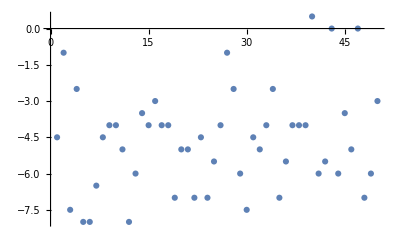

```mathematica
ListPlot[EnergyList[CellularAutomaton[110,RandomInteger[{0,1},100],50]],PlotRange->All]
```

```mathematica
elist=1/10000 Sum[N@EnergyList[CellularAutomaton[110,RandomInteger[{0,1},100],50]],{10000}]
```

{-6.2327,-1.566,-5.4855,-6.479,-5.32265,-6.512,-5.5659,-5.17185,-5.25815,-5.5135,-5.20235,-4.84115,-5.26635,-5.03075,-4.73765,-4.8768,-4.73005,-4.64905,-4.62335,-4.67275,-4.6285,-4.55435,-4.5702,-4.6132,-4.5538,-4.487,-4.5642,-4.51925,-4.4999,-4.5136,-4.55395,-4.46715,-4.44685,-4.47905,-4.4626,-4.4221,-4.43645,-4.4296,-4.36265,-4.3892,-4.40055,-4.3605,-4.38365,-4.38715,-4.3716,-4.28055,-4.30705,-4.3579,-4.30245,-4.2936}

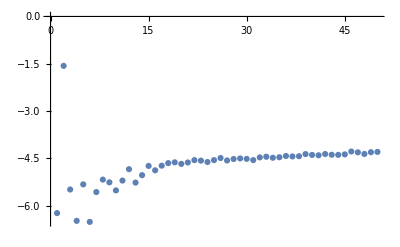

```mathematica
ListPlot[elist]
```

```mathematica
ArrayPlot[CellularAutomaton[110,RandomInteger[{0,1},100],100]]
```

-Graphics-